```mathematica
Sin[x]
```

Sin[x]

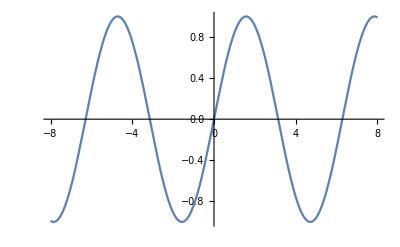

```mathematica
Plot[Sin[x],{x,-8,8}]
```

```mathematica
FullSimplify[ArcCurvature[{x,Sin[x]},x],x∈Reals]
```

Abs[Sin[x]]/((1+Cos[x]^2)^(3/2))

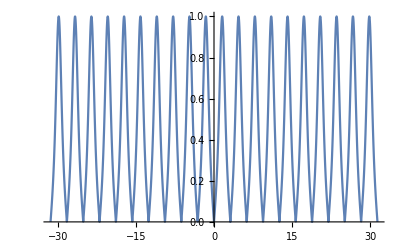

```mathematica
Plot[Abs[Sin[x]]/((1+Cos[x]^2)^(3/2)),{x,-10 π,10 π}]
```

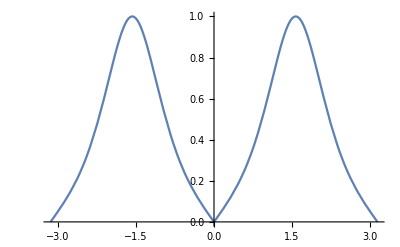

```mathematica
Plot[Abs[Sin[x]]/((1+Cos[x]^2)^(3/2)),{x,-π, π}]
```

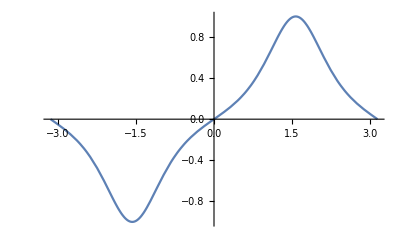

```mathematica
Plot[Sin[x]/((1+Cos[x]^2)^(3/2)),{x,-π, π}]
```

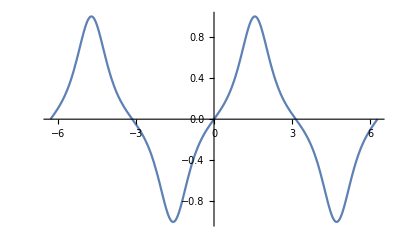

```mathematica
Plot[Sin[x]/((1+Cos[x]^2)^(3/2)),{x,-2π,2 π}]
```

```mathematica
Sin[x+2π]
```

Sin[x]

```mathematica
Integrate[Sin[x],{x,0,2π}]
```

0

```mathematica
Integrate[Sin[x],{x,a,a+2π}]
```

0

```mathematica
Series[Sin[x],{x,0,3}]
```

x-x^3/6+O[x]^4

```mathematica
Series[Sin[x],{x,0,4}]
```

x-x^3/6+O[x]^5

```mathematica
Normal[x-x^3/6+O[x]^5]
```

x-x^3/6

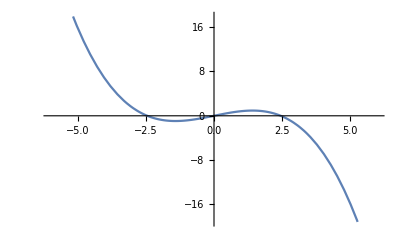

```mathematica
Plot[x-x^3/6,{x,-5.999999999999999,5.999999999999999}]
```

```mathematica
FullForm[x-x^3/6+O[x]^5]
```

SeriesData[x,0,List[1,0,Rational[-1,6]],1,5,1]

```mathematica
Series[Sin[x],{x,0,5}]
```

x-x^3/6+x^5/120+O[x]^6

```mathematica
Normal[x-x^3/6+x^5/120+O[x]^6]
```

x-x^3/6+x^5/120

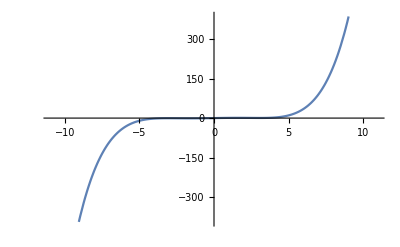

```mathematica
Plot[x-x^3/6+x^5/120,{x,-10.954451150103322,10.954451150103322}]
```

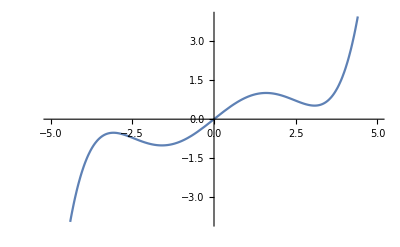

```mathematica
Plot[x-x^3/6+x^5/120,{x,-5,5}]
```

```mathematica
Series[Sin[x],{x,0,7}]
```

x-x^3/6+x^5/120-x^7/5040+O[x]^8

```mathematica
Normal[x-x^3/6+x^5/120-x^7/5040+O[x]^8]
```

x-x^3/6+x^5/120-x^7/5040

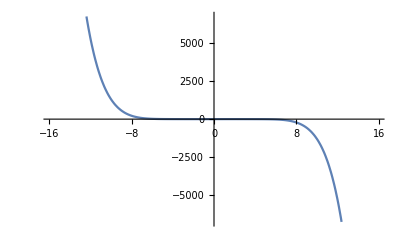

```mathematica
Plot[x-x^3/6+x^5/120-x^7/5040,{x,-15.874507866387544,15.874507866387544}]
```

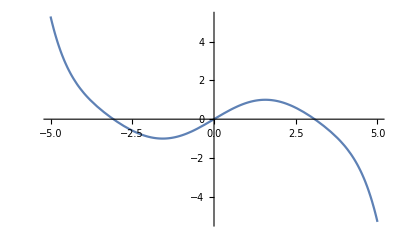

```mathematica
Plot[x-x^3/6+x^5/120-x^7/5040,{x,-5,5}]
```

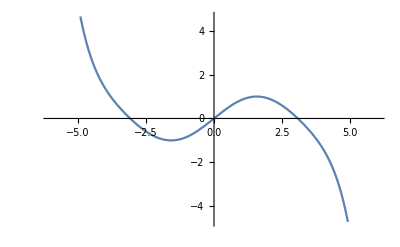

```mathematica
Plot[x-x^3/6+x^5/120-x^7/5040,{x,-6,6}]
```

```mathematica
Series[Sin[x],{x,0,9}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^10

```mathematica
Normal[x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^10]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

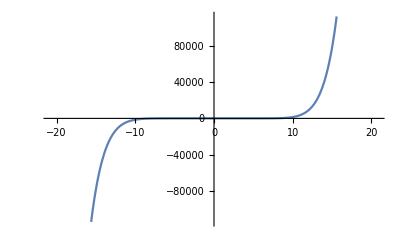

```mathematica
Plot[x-x^3/6+x^5/120-x^7/5040+x^9/362880,{x,-20.784609690826528,20.784609690826528}]
```

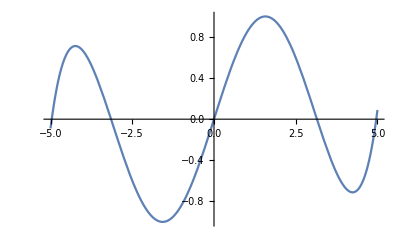

```mathematica
Plot[x-x^3/6+x^5/120-x^7/5040+x^9/362880,{x,-5,5}]
```

```mathematica
FullForm[Out[25]]
```

SeriesData[x,0,List[1,0,Rational[-1,6],0,Rational[1,120],0,Rational[-1,5040],0,Rational[1,362880]],1,10,1]

```mathematica
SeriesData[x,Pi,List[1,0,Rational[-1,6],0,Rational[1,120],0,Rational[-1,5040],0,Rational[1,362880]],1,10,1]
```

(x-π)-1/6 (x-π)^3+1/120 (x-π)^5-(x-π)^7/5040+(x-π)^9/362880+O[x-π]^10

```mathematica
Normal[(x-π)-1/6 (x-π)^3+1/120 (x-π)^5-(x-π)^7/5040+(x-π)^9/362880+O[x-π]^10]
```

-π+x-1/6 (-π+x)^3+1/120 (-π+x)^5-(-π+x)^7/5040+(-π+x)^9/362880

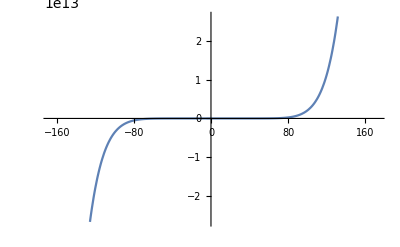

```mathematica
Plot[-π+x-1/6 (-π+x)^3+1/120 (-π+x)^5-(-π+x)^7/5040+(-π+x)^9/362880,{x,-166.50441064025907,172.78759594743863}]
```

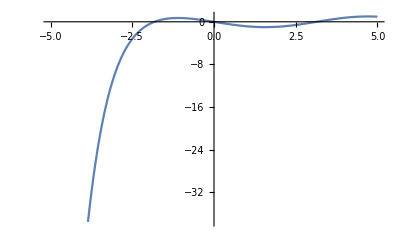

```mathematica
Plot[-π+x-1/6 (-π+x)^3+1/120 (-π+x)^5-(-π+x)^7/5040+(-π+x)^9/362880,{x,-5,5}]
```

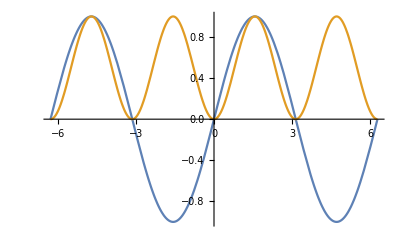

```mathematica
Plot[{Sin[x],Sin[x]^2},{x,-2π,2π}]
```

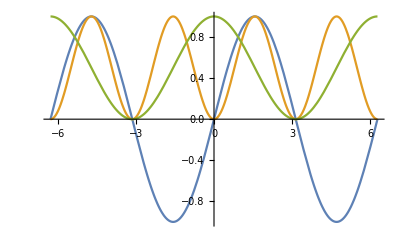

```mathematica
Plot[{Sin[x],Sin[x]^2,(1+Cos[x])/2},{x,-2π,2π}]
```

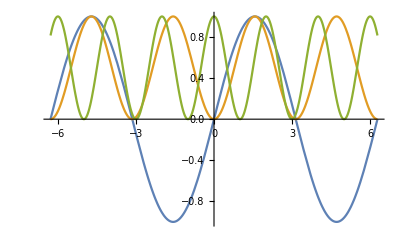

```mathematica
Plot[{Sin[x],Sin[x]^2,(1+Cos[π x])/2},{x,-2π,2π}]
```

```mathematica
1/x
```

1/x

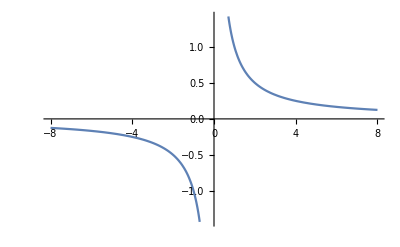

```mathematica
Plot[1/x,{x,-8,8}]
```

```mathematica
Integrate[1/x,{x,-1,1}]
```

Integrate::idiv: Integral of 1/x does not converge on {-1,1}.

∫_-1^1 1/x ⅆx

```mathematica
Exp[f'[x]/f[x]]
```

ⅇ^(f'[x]/f[x])

```mathematica
With[{f=Log},
Exp[f'[x]/f[x]]
]
```

ⅇ^(1/(x Log[x]))

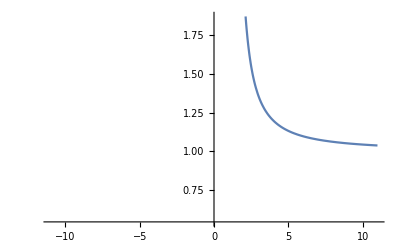

```mathematica
Plot[ⅇ^(1/(x Log[x])),{x,-11.,11.}]
```

```mathematica
With[{f=Exp},
Exp[f'[x]/f[x]]
]
```

ⅇ

```mathematica
Exp[f'[x]/f[x]]==x
```

ⅇ^(f'[x]/f[x])==x

```mathematica
DSolve[ⅇ^(f'[x]/f[x])==x,{f[x]},{x}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f[x]→ⅇ^(-x+x Log[x]) C[1]}}

```mathematica
With[{f=Function[x,ⅇ^(-x+x Log[x])]},
Exp[f'[x]/f[x]]
]
```

x

```mathematica
ⅇ^(-x+x Log[x])
```

ⅇ^(-x+x Log[x])

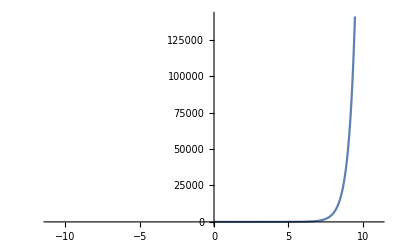

```mathematica
Plot[ⅇ^(-x+x Log[x]),{x,-11.,11.}]
```

```mathematica
1/x
```

1/x

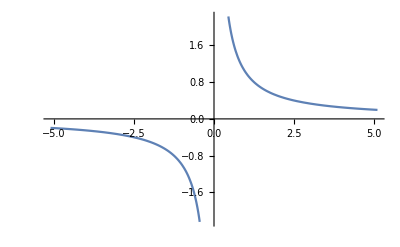

```mathematica
Plot[1/x,{x,-5.1,5.1}]
```

```mathematica
FullSimplify[ArcCurvature[{x,1/x},x],x∈Reals]
```

(2 Abs[x]^3)/((1+x^4)^(3/2))

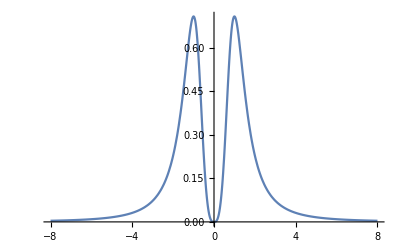

```mathematica
Plot[(2 Abs[x]^3)/((1+x^4)^(3/2)),{x,-8,8}]
```

```mathematica
Limit[(2 Abs[x]^3)/((1+x^4)^(3/2)),x->∞]
```

0

```mathematica
(1+x^4)^(3/2)==0
```

(1+x^4)^(3/2)==0

```mathematica
Reduce[(1+x^4)^(3/2)==0]
```

x==-(-1)^(1/4)||x==(-1)^(1/4)||x==-(-1)^(3/4)||x==(-1)^(3/4)

```mathematica
FindInstance[(1+x^4)^(3/2)==0,{x}]
```

{{x→Root-0.707-0.707 ⅈRoot[1+#1^4&,1]-0.7071067811865476}}

```mathematica
Integrate[(2 Abs[x]^3)/((1+x^4)^(3/2)),{x,-∞,∞}]
```

2

```mathematica
FullSimplify[ArcCurvature[{x,ⅇ^(-x+x Log[x])},x],x∈Reals]
```

ⅇ^(2 x) √((x^(-2+2 x) (1+x Log[x]^2)^2)/((ⅇ^(2 x)+x^(2 x) Log[x]^2)^3))

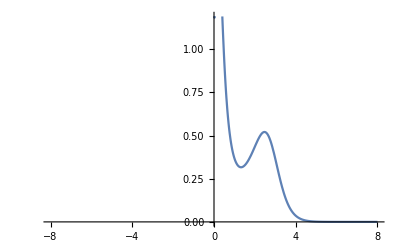

```mathematica
Plot[ⅇ^(2 x) √((x^(-2+2 x) (1+x Log[x]^2)^2)/((ⅇ^(2 x)+x^(2 x) Log[x]^2)^3)),{x,-8,8}]
```

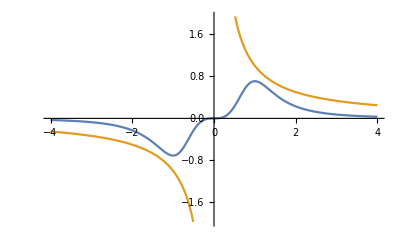

```mathematica
Plot[{(2 x^3)/((1+x^4)^(3/2)),1/x},{x,-4,4}]
```

```mathematica
FullSimplify[ArcCurvature[{x,f[x]},x],{x,f[x]}∈Reals]
```

√(f''[x]^2/((1+f'[x]^2)^3))

```mathematica
FullSimplify[ArcCurvature[{x,f[x]},x],{x,f[x]}∈Reals]==g[x]
```

√(f''[x]^2/((1+f'[x]^2)^3))==g[x]

```mathematica
DSolve[√(f''[x]^2/((1+f'[x]^2)^3))==g[x],{f[x],f[x]},{x}]
```

{{f[x]→C[2]+-(ⅈ (C[1]+-g[K[1]]K[1]1K[3]))/(√(-1+C[1]^2+2 C[1] -g[K[1]]K[1]1K[3]+(-g[K[1]]K[1]1K[3])^2))K[3]1x},{f[x]→C[2]+(ⅈ (C[1]+-g[K[1]]K[1]1K[4]))/(√(-1+C[1]^2+2 C[1] -g[K[1]]K[1]1K[4]+(-g[K[1]]K[1]1K[4])^2))K[4]1x},{f[x]→C[2]+-(ⅈ (C[1]+g[K[2]]K[2]1K[5]))/(√(-1+C[1]^2+2 C[1] g[K[2]]K[2]1K[5]+(g[K[2]]K[2]1K[5])^2))K[5]1x},{f[x]→C[2]+(ⅈ (C[1]+g[K[2]]K[2]1K[6]))/(√(-1+C[1]^2+2 C[1] g[K[2]]K[2]1K[6]+(g[K[2]]K[2]1K[6])^2))K[6]1x}}

```mathematica
DSolve[√(f''[x]^2/((1+f'[x]^2)^3))==g[x],f[x],{x}]
```

{{f[x]→C[2]+-(ⅈ (C[1]+-g[K[1]]K[1]1K[3]))/(√(-1+C[1]^2+2 C[1] -g[K[1]]K[1]1K[3]+(-g[K[1]]K[1]1K[3])^2))K[3]1x},{f[x]→C[2]+(ⅈ (C[1]+-g[K[1]]K[1]1K[4]))/(√(-1+C[1]^2+2 C[1] -g[K[1]]K[1]1K[4]+(-g[K[1]]K[1]1K[4])^2))K[4]1x},{f[x]→C[2]+-(ⅈ (C[1]+g[K[2]]K[2]1K[5]))/(√(-1+C[1]^2+2 C[1] g[K[2]]K[2]1K[5]+(g[K[2]]K[2]1K[5])^2))K[5]1x},{f[x]→C[2]+(ⅈ (C[1]+g[K[2]]K[2]1K[6]))/(√(-1+C[1]^2+2 C[1] g[K[2]]K[2]1K[6]+(g[K[2]]K[2]1K[6])^2))K[6]1x}}

```mathematica
Dt[f[x]]
```

Dt[x] f'[x]

```mathematica
Dt[f[x]]^2
```

Dt[x]^2 f'[x]^2

```mathematica
FourierSeries[x]
```

FourierSeries::argmu: FourierSeries called with 1 argument; 3 or more arguments are expected.

FourierSeries[x]

```mathematica
FourierSeries[t,t,1]
```

ⅈ ⅇ^(-ⅈ t)-ⅈ ⅇ^(ⅈ t)

```mathematica
ExpToTrig[ⅈ ⅇ^(-ⅈ t)-ⅈ ⅇ^(ⅈ t)]
```

2 Sin[t]

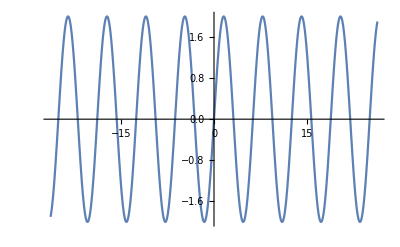

```mathematica
Plot[2 Sin[t],{t,-26.389378290154262,26.389378290154262}]
```

```mathematica
FourierSeries[t,t,2]
```

ⅈ ⅇ^(-ⅈ t)-ⅈ ⅇ^(ⅈ t)-1/2 ⅈ ⅇ^(-2 ⅈ t)+1/2 ⅈ ⅇ^(2 ⅈ t)

```mathematica
ExpToTrig[ⅈ ⅇ^(-ⅈ t)-ⅈ ⅇ^(ⅈ t)-1/2 ⅈ ⅇ^(-2 ⅈ t)+1/2 ⅈ ⅇ^(2 ⅈ t)]
```

2 Sin[t]-Sin[2 t]

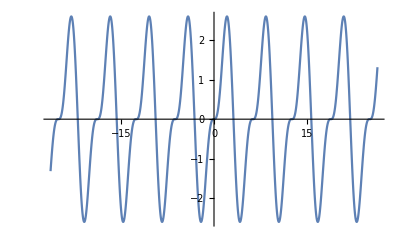

```mathematica
Plot[2 Sin[t]-Sin[2 t],{t,-26.389378290154262,26.389378290154262}]
```

```mathematica
FourierSeries[t,t,10]
```

ⅈ ⅇ^(-ⅈ t)-ⅈ ⅇ^(ⅈ t)-1/2 ⅈ ⅇ^(-2 ⅈ t)+1/2 ⅈ ⅇ^(2 ⅈ t)+1/3 ⅈ ⅇ^(-3 ⅈ t)-1/3 ⅈ ⅇ^(3 ⅈ t)-1/4 ⅈ ⅇ^(-4 ⅈ t)+1/4 ⅈ ⅇ^(4 ⅈ t)+1/5 ⅈ ⅇ^(-5 ⅈ t)-1/5 ⅈ ⅇ^(5 ⅈ t)-1/6 ⅈ ⅇ^(-6 ⅈ t)+1/6 ⅈ ⅇ^(6 ⅈ t)+1/7 ⅈ ⅇ^(-7 ⅈ t)-1/7 ⅈ ⅇ^(7 ⅈ t)-1/8 ⅈ ⅇ^(-8 ⅈ t)+1/8 ⅈ ⅇ^(8 ⅈ t)+1/9 ⅈ ⅇ^(-9 ⅈ t)-1/9 ⅈ ⅇ^(9 ⅈ t)-1/10 ⅈ ⅇ^(-10 ⅈ t)+1/10 ⅈ ⅇ^(10 ⅈ t)

```mathematica
ExpToTrig[%74]
```

2 Sin[t]-Sin[2 t]+2/3 Sin[3 t]-1/2 Sin[4 t]+2/5 Sin[5 t]-1/3 Sin[6 t]+2/7 Sin[7 t]-1/4 Sin[8 t]+2/9 Sin[9 t]-1/5 Sin[10 t]

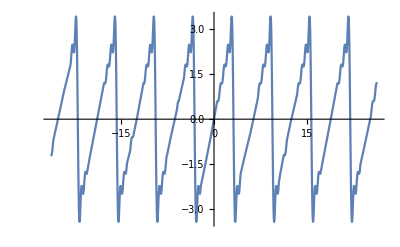

```mathematica
Plot[2 Sin[t]-Sin[2 t]+2/3 Sin[3 t]-1/2 Sin[4 t]+2/5 Sin[5 t]-1/3 Sin[6 t]+2/7 Sin[7 t]-1/4 Sin[8 t]+2/9 Sin[9 t]-1/5 Sin[10 t],{t,-26.389378290154262,26.389378290154262}]
```

```mathematica
ComplexPlot[ⅈ ⅇ^(-ⅈ t)-ⅈ ⅇ^(ⅈ t),{t,-1-I,1+I}]
```

-Graphics-

```mathematica
ComplexPlot[t,{t,-1-I,1+I}]
```

-Graphics-

```mathematica
ComplexPlot[1/t,{t,-1-I,1+I}]
```

-Graphics-

```mathematica
Limit[FourierSeries[t,t,a],a->∞]
```

lim_(a→∞) FourierSeries[t,t,a]